# Model for Sport WSS24 Project

## Utilities

```mathematica
ResourceFunction["DarkMode"][]
ClearAll["Global`*"]
```

## Graph of Basketball Offense 6/21

```mathematica
getPathEdges[path_]:=Module[{result = {}},For[i=1, i< Length[path],i+=1, AppendTo[result, path[[i]]->path[[i+1]]]]; result]
topKey = {3, 0};
rightWing = {4.5, 0.625};
leftWing = {1.5, 0.625};
leftCorner = {1.25, 2};
rightCorner =  {4.75, 2};
highPost = {3, 0.75};
hoop = {3, 2};
edges = {topKey->leftWing,  topKey->rightWing,  topKey->highPost,topKey->hoop, leftWing->leftCorner, leftWing->highPost,leftWing->topKey, leftWing->hoop, rightWing->topKey, rightWing->highPost,rightWing->rightCorner, rightWing->hoop, highPost->hoop, highPost->leftWing, highPost->leftCorner,highPost->rightWing,highPost->rightCorner, highPost->topKey, leftCorner->hoop, leftCorner->leftWing, leftCorner->highPost, rightCorner->hoop, rightCorner->highPost, rightCorner->rightWing};
allSpots = {topKey, rightWing, leftWing, leftCorner, rightCorner,highPost, hoop};
```

```mathematica
halfCourt = Graph[allSpots, edges, VertexCoordinates->allSpots, GraphHighlight->{hoop}]
```

-Graphics-

```mathematica
maxPasses = 2;
start = highPost;
```

```mathematica
Dynamic[
pathList = FindPath[halfCourt,start,hoop,maxPasses, 10];
pathEdgesList = getPathEdges/@ pathList;
HighlightGraph[halfCourt, Style[#, Purple, Thick]&/@Flatten[pathEdgesList, 1]]
]
```

## Full-court Basketball Graph 6/23

### Functions

```mathematica
getPointsWithinDistance[start_,dests_, distance_]:=Select[dests,EuclideanDistance[#,start]<=distance&& #!=start&]
getEdges[source_, dests_]:= source->#&/@ DeleteCases[dests, source];
getEdgesAll[sources_, dest_]:= #->dest&/@ sources;
getPathEdges[path_]:=Module[{result = {}},For[i=1, i< Length[path],i+=1, AppendTo[result, path[[i]]->path[[i+1]]]]; result]
```

### Court Dimensions

This is approximately the real court dimensions

```mathematica
courtWidth = 53;
courtLength = 95;
```

### Set location of objects and spots on the court

```mathematica
topKey = {27, 61};
leftWing = {9, 75};
rightWing = {47, 75};
rightCorner = {47, 89};
leftCorner = {7, 89};
p1 = topKey;
p2 = leftWing ;
p3 = rightWing;
p4 = rightCorner;
p5 = leftCorner;
homePlayers = {p1, p2, p3, p4, p5};
possessorOfBall = p1;
hoopAway = {27, 89};
hoopHome = {27, 5};
hoops = {hoopHome, hoopAway};
```

### Determine which players are immediate threats

This pass and shot length is based on my estimate of what would generally occur in a game

```mathematica
maxPassLength =50;
maxShotLength = 23;
```

Getting players that are immediate threats

```mathematica
playersWithin1Pass= getPointsWithinDistance[ball,homePlayers, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,homePlayers, maxShotLength];
threatPlayers =Intersection[playersWithin1Pass, playersInShotRange];
```

Drawing pass and shot edges

```mathematica
passes = getEdges[ball, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
```

### Graphing the game

This is approximately real-size with some minor modifications so that I have a middle column. The blue lines are potential passes and the red lines are potential shots. You can adjust the max pass and shot length to get different results

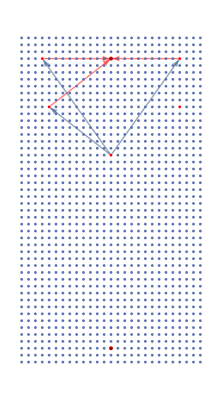

```mathematica
vertices = Table[{i, j}, {i, 1, courtWidth, 2}, {j, 1, courtLength, 2}];
toHighlight ={hoopHome, hoopAway};
fullCourt = Graph[Flatten[vertices, 1],Join[passes, shotsStyled], VertexCoordinates->Flatten[vertices, 1], GraphHighlight->toHighlight, VertexSize->Large,  VertexStyle->Map[#->Red&, homePlayers]]
```

Assessing the quality of a position

```mathematica
numAttackVectors = Length[shots];
```

Okay so finally what I have here is a single metric for how spread out the players are. What I do is simply take the log of the differences of all the x coordinates, then do the same with y, then sum it all up. I tried using variance, std,mad initially, but the issue was that all three gave too much weight to large variations for my liking. In the game, it is better to have all your players spread out a little bit then one player spread out a lot. So I needed to weight the large variations lower. This is the reason  for the log. The one issue with this method was that if the differences were 0 the log gives -oo so if it is 0 I just set the value to 0 and don’t take the log to work around this. Here is a manipulate to play around with player positions and see how it affects the metric. It looks good to me so far.

```mathematica
Manipulate[Module[{players,diffsX, diffsY, logDifferencesX, logDifferencesY, playersWithin1Pass, playersInShotRange, threatPlayers, passes, shots, shotsStyled, fullCourt, toEnlarge, spreadFactor, numAttackVectors},
players = {pt1,pt2, pt3, pt4, pt5};
playersWithin1Pass= getPointsWithinDistance[ball,players, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,players, maxShotLength];
threatPlayers =Intersection[playersWithin1Pass, playersInShotRange]; 
passes = getEdges[ball, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
toEnlarge = #->1&/@ players;
fullCourt = Graph[
Flatten[vertices, 1],
Join[passes, shotsStyled], 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  VertexSize->toEnlarge
 ];
diffsX = Differences[players[[All, 1]]];
diffsY = Differences[players[[All, 2]]];logDifferencesX=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsX;logDifferencesY=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsY;
spreadFactor = N@Total[{Total[logDifferencesX], Total[logDifferencesY]}];
numAttackVectors = Length[shots];
Column[{fullCourt, spreadFactor, numAttackVectors}]
],
Row[
{Control[{pt1,{1, 1}, { 54, 95}, {2,2}}], 
Control[{pt2,{1, 1}, { 54, 95}, {2,2}}], 
Control[{pt3,{1, 1}, { 54, 95}, {2, 2}}], 
Control[{pt4,{1, 1}, { 54, 95}, {2, 2}}], 
Control[{pt5,{1, 1}, { 54, 95}, {2, 2}}]}]]
```

The next step is to have the manipulate show the graph. First what I need is to have the sliders have jumps of 2 instead of 1.

It’s too slow when I edit directly in the graph, I’m going to set the variables here and then run the graph after

```mathematica
{
Slider2D[Dynamic[pt1], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt1], 
Slider2D[Dynamic[pt2], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt2],
Slider2D[Dynamic[pt3], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt3],
Slider2D[Dynamic[pt4], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt4],
Slider2D[Dynamic[pt5], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt5]
}
```

{,,,,,,,,,}

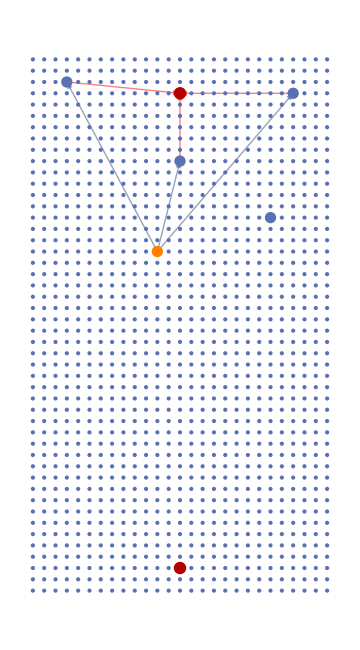
-Graphics-
19.8795
3

```mathematica
players = {pt1, pt2, pt3, pt4, pt5};
possessorOfBall = pt1;
playersWithin1Pass= getPointsWithinDistance[possessorOfBall,players, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,players, maxShotLength];
threatPlayers =If[MemberQ[playersInShotRange, possessorOfBall], Append[Intersection[playersWithin1Pass, playersInShotRange],possessorOfBall], Intersection[playersWithin1Pass, playersInShotRange]];
passes = getEdges[possessorOfBall, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
toEnlarge = Join[#->1&/@ Join[players, hoops]];
diffsX = Differences[players[[All, 1]]];
diffsY = Differences[players[[All, 2]]];logDifferencesX=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsX;logDifferencesY=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsY;
spreadFactor = N@Total[{Total[logDifferencesX], Total[logDifferencesY]}];
numAttackVectors = Length[shots];
Column[{fullCourt = Graph[
Flatten[vertices, 1],
Join[passes, shotsStyled], 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  VertexSize->toEnlarge, ImageSize->Medium, VertexStyle->{possessorOfBall->Orange}
 ],
spreadFactor,
numAttackVectors}
]
```

Okay so above we have a a way to visualize and evaluate the quality of a position in basketball

The next step is to evaluate not just the snap shot of the position but start to incorporate how the position can morph into other positions. Let’s allow for dribbling within a certain radius and then make the pass and shot edges  be dashed and dribbling be dotted I guess I’ll see

Idea: What games would not lead to caring about the middle. Well baseball. Any goal sports. List of goal sports: basketball, football, soccer, chess, hockey, etc. This gives you optionality which gives you control. Another idea is to have

Another idea is the preference for bottom up rules. In the NBA they’re tending to not have plays. In soccer they don’t have plays. Why this process as opposed to a top down mechanism?

Okay first I want to show the number of places you can go as you change the location.

Let’s state the laws and see if the model captures those laws

### Law #1: The middle is advantageous proportional to the speed of the ball

Up to the limit of the court size

and maybe inversely proportional to the ratio of the shot range to the size of the court but I have to think about how the importance of the middle is impacted by shot range and court size

```mathematica
{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1], Slider[Dynamic[speedOfBall], {1, 30}], Dynamic[speedOfBall]}
```

{,,,}

```mathematica
(*shotRange= getPointsWithinDistance[hoopAway, Flatten[vertices, 1], *)
passablePoints  = getPointsWithinDistance[pt1, Flatten[vertices, 1], speedOfBall];
passableEdges = getEdges[pt1, passablePoints];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
toEnlarge = #->1&/@ Join[hoops, {pt1}];
Graph[
Flatten[vertices, 1],
passableEdges, 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[vertices,1].

Flatten::flev: The level argument 1→0.5 in position 2 of Flatten[vertices→0.5,1→0.5] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[vertices,1].

Join::heads: Heads Flatten and Rule at positions 1 and 2 are expected to be the same.

Graph[Flatten[vertices,1],getEdges[{39,39},getPointsWithinDistance[{39,39},Flatten[vertices,1],1.]],VertexCoordinates→Flatten[vertices,1],GraphHighlight→toHighlight,ImageSize→Medium,VertexSize→Join[Flatten[vertices→0.5,1→0.5],Rule[hoops,1,{{39,39}},1]]]

In games where kids aren’t able to throw long passes and the speed of the ball is really slow, it doesn’t actually help to get the ball to the middle that much because they can’t take advantage of it with long passes

### Law #2: The dispersion of players is directly proportional to the speed of the ball

One constraint on this is it only works when the ball moves faster than the player. Otherwise there is no advantage to passing over dribbling

You see this in kids soccer where because they don’t have the ability to pass the ball quickly and accurately, there is no advantage to spreading out

Let’s forget about the hoops for a second. The reason it makes sense to do this is because its about getting the ball in dangerous positions. The way to do that is to maximize the number of points you can access and therefore maximize the number of paths to the basket and the variance of those paths. It seems like to me there are two reasons for why variance is advantageous. One is you minimize overlap and another reason is you maximize the variance of your attack vectors

Let’s add one player. Where should we put him. Any point where the distance to the original point is equal to the speed of the ball

#### Adding one player

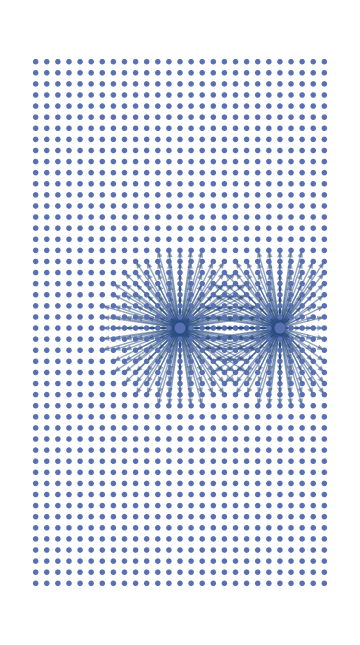
{-Graphics-,277}

```mathematica
passablePoints  = getPointsWithinDistance[pt1, Flatten[vertices, 1], speedOfBall];
passableEdges = getEdges[pt1, passablePoints];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
passablePointspt2 = getPointsWithinDistance[pt2,Flatten[vertices, 1], speedOfBall];
passableEdgespt2 = getEdges[pt2, passablePointspt2];
toEnlarge = {pt1->1, pt2->1};
{Graph[
Flatten[vertices, 1],
Join[passableEdges, passableEdgespt2], 
VertexCoordinates->Flatten[vertices, 1],ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
], Length[Union[Join[passablePoints, passablePointspt2]]]}
```

The court coverage is measured by the number of points reached:

507

```mathematica
{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1],Slider2D[Dynamic[pt2], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt2], Slider[Dynamic[speedOfBall], {1, 30, 1}], Dynamic[speedOfBall]}
```

{,,,,,}

```mathematica
potentialPoints =
```

#### Adding 5 players

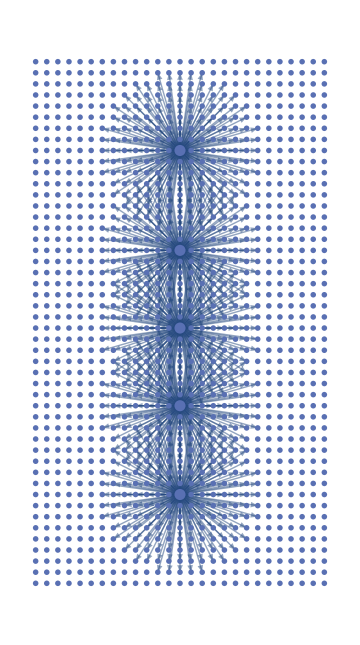
{-Graphics-,618}

```mathematica
players = {pt1, pt2, pt3, pt4, pt5};
passablePointsList  = getPointsWithinDistance[#, Flatten[vertices, 1], speedOfBall]&/@ players;
passableEdgesList = MapThread[getEdges[#1, #2]&, {players, passablePointsList}];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
toEnlarge = #->1&/@ players;
{Graph[
Flatten[vertices, 1],
Flatten[passableEdgesList, 1], 
VertexCoordinates->Flatten[vertices, 1],ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
], Length[Union[Flatten[passablePointsList, 1]]]}
```

The court coverage is measured by the number of points reached:

507

```mathematica
Grid[{{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1],Slider2D[Dynamic[pt2], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt2], 
Slider2D[Dynamic[pt3], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt3]}, 
{Slider2D[Dynamic[pt4], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt4], 
Slider2D[Dynamic[pt5], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt5], 
Slider[Dynamic[speedOfBall], {1, 30, 1}], Dynamic[speedOfBall]}}]
```

|  |  |  |  | 
 |  |  |  |  |

Okay so what’s bugging me about the above model is that you would never want to line up your players like that. I thought about it for a while and the reason is that you care more about the space near the ball then the space away from the ball. But I don’t want to add complexity to the mode. This model captures two of my initial ideas, first being that the middle is more valuable then the edges and the second is that players tend to spread out.

## Circular Passing Microstructure

### Core functionality

#### Neutral graphics

```mathematica
ballPoint = {0,0}
maxPassLength = 20
maxPassRing = Circle[ballPoint, maxPassLength]
neutralGraphics = {neutralColor, PointSize[0.05],Point[ballPoint], maxPassRing}
```

{0,0}

20

Circle[{0,0},20]

{RGBColor[0.39542229343099106, 0.2037842374303807, 0.006607156481269551],PointSize[0.05],Point[{0,0}],Circle[{0,0},20]}

#### Defensive graphics

This is proportional to the speed of the defender:

```mathematica
defenderArcAngles= {{Pi/8,3Pi/8}, {5Pi/8,7Pi/8}}
```

{{π/8,(3 π)/8},{(5 π)/8,(7 π)/8}}

```mathematica
defenderArcs= Circle[ballPoint,maxPassLength, #]&/@defenderArcAngles
defensiveGraphics= Join[{defensiveColor,  Thickness[0.025],Opacity[0.3]}, defenderArcs]
```

{Circle[{0,0},20,{π/8,(3 π)/8}],Circle[{0,0},20,{(5 π)/8,(7 π)/8}]}

{RGBColor[0.7877775234607461, 0.01850919356069276, 0.018326085297932403],Thickness[0.025],Opacity[0.3],Circle[{0,0},20,{π/8,(3 π)/8}],Circle[{0,0},20,{(5 π)/8,(7 π)/8}]}

#### Offensive graphics

```mathematica
attackerPoints ={{-20, 15}, {-5, 16},{19, 19}} 
offensiveGraphics = {offensiveColor,PointSize[0.05], Point/@ attackerPoints}
```

{{-20,15},{-5,16},{19,19}}

{RGBColor[0.30214389257648583, 0.5284962233920806, 0.010528725108720532],PointSize[0.05],{Point[{-20,15}],Point[{-5,16}],Point[{19,19}]}}

#### Visualization

Now let’s graph all these objects

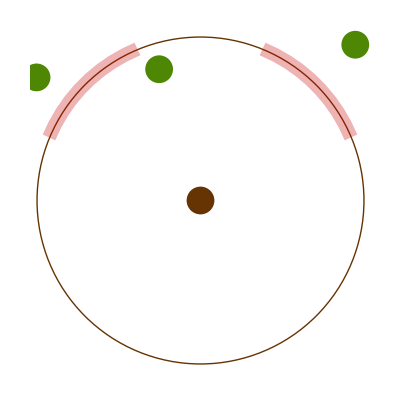

```mathematica
Graphics[{neutralGraphics, defensiveGraphics, offensiveGraphics} ]
```

## 1d Model Implementation

### Initializing

{{1,1},{2,1},{2,6},{2,11}}

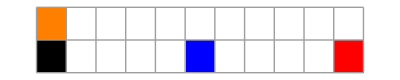

```mathematica
gameLength = 11;
emptyGameArray = ConstantArray[0, {2, gameLength}];
qbIdx = {2, 1};
attackerIdx = {2, 6};
defenderIdx = {2, 11};
ballIdx = {1, 1};
ballSpeed = 1;
playerSpeed = 1;
reactionTime = 0;
playerIdxs = {ballIdx, qbIdx, attackerIdx, defenderIdx}
playerRules = {qbIdx->Black, ballIdx->Orange, attackerIdx->Blue, defenderIdx->Red};
initialGameArray = ReplacePart[emptyGameArray,playerRules];
colorRules = {qb->Black, attacker->Blue, defender->Red, ball->Orange};
ArrayPlot[initialGameArray, Mesh->True,ColorRules->colorRules ]
```

### Passing

```mathematica
throwBall1Step[ballIdx_]:= 
ballIdx->1
```

```mathematica
passLength = 5
ballPassIdxs = NestList[throwBall1Step, ballIdx, passLength]
```

5

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}}

```mathematica
getPassArray = Replace[playerIdxs, ]
```

## Styling

```mathematica
ColorSetter[Dynamic[offensiveColor]]
```

$CellContext`offensiveColor

```mathematica
ColorSetter[Dynamic[defensiveColor]]
```

$CellContext`defensiveColor

```mathematica
ColorSetter[Dynamic[neutralColor]]
```

$CellContext`neutralColor

## Scratchpad

```mathematica
testRules = {1->a, 2->b}
```

{1→a,2→b}

```mathematica
testRules/.Rule->List
```

{{1,a},{2,b}}

```mathematica
testRuleList = ReplaceAll[testRules, Rule->List]
```

{{1,a},{2,b}}

```mathematica
Replace[testRuleList, List->Rule, {1}]
```

{{1,a},{2,b}}